```mathematica
SetOptions[NSolve,WorkingPrecision->100]
```

{WorkingPrecision→100,Sort→True,MonomialOrder→Automatic,Method→Automatic}

## Functions Used to Study Roots of Partial Sums

### This contains the definitions of RootsOfPartial, ListRootsOfPartial and RootsPlot

RootsOfPartial outputs a list of complex roots of the nth partial sum of expr in terms of complex coordinates

```mathematica
RootsOfPartial[expr_,z_,n_]:=Module[{roots,poly},
poly = Normal[Series[expr,{z,0,n}]];
roots = z/. NSolve[poly==0,z]
]
```

ListRootsOfPartial gives the Roots of the nth partial sum of expr in list form, where 1st coordinate is the real part and the 2nd coordinate is the Imaginary coordinate

```mathematica
ListRootsOfPartial[expr_,z_,n_]:=Module[{roots},
roots = RootsOfPartial[expr,z,n];
roots = Transpose[{Re[roots],Im[roots]}]
]
```

RootsPlot output a graphic of the roots of the nth partial sum of expr

```mathematica
RootsPlot[expr_,z_,n_]:=Module[{roots,size,list},
 roots = RootsOfPartial[expr,z,n];
size = Max[Abs[roots]];
list = Transpose[{Re[roots],Im[roots]}];
ListPlot[list,
PlotStyle->PointSize[.02],
PlotRange->{{-1-size,1+size},{-1-size,1+size}},
AspectRatio->Automatic]]
```

Sometimes a function is given just as a Taylor Series Around zeros so the functions PolyRoots, PolyListRoots and PolyPlotRoots are the analogous functions to the above only they read in polynomials

```mathematica
RootsOfPoly[poly_,z_]:=z/.NSolve[poly==0,z]

ListRootsOfPoly[poly_,z_] := Module[{roots},
roots = PolyRoots[poly,z];
roots =Transpose[{Re[roots],Im[roots]}]
]

RootsPlotOfPoly[poly_,z_]:=Module[{roots,size},
roots = PolyRoots[poly,z];
size = Max[Abs[roots]];
roots = Transpose[{Re[roots],Im[roots]}];
ListPlot[roots,
PlotRange->{{-1-size,1+size},{-1-size,1+size}},
AspectRatio->Automatic,
PlotStyle->{PointSize[.02]}
]
]
```

#### An Example: Application to the Exponential Function

Here is an example of these functions for the exponential function :

```mathematica
Exp[z]
exppoly10=Normal[Series[Exp[z],{z,0,10}]]
```

ⅇ^z

1+z+z^2/2+z^3/6+z^4/24+z^5/120+z^6/720+z^7/5040+z^8/40320+z^9/362880+z^10/3628800

```mathematica
RootsOfPartial[Exp[z],z,10]
ListRootsOfPartial[Exp[z],z,10]
```

{-3.55388-0.789422 ⅈ,-3.55388+0.789422 ⅈ,-3.01554-2.33522 ⅈ,-3.01554+2.33522 ⅈ,-1.87166-3.77019 ⅈ,-1.87166+3.77019 ⅈ,0.0662015-4.96768 ⅈ,0.0662015+4.96768 ⅈ,3.37487-5.62602 ⅈ,3.37487+5.62602 ⅈ}

{{-3.55388,-0.789422},{-3.55388,0.789422},{-3.01554,-2.33522},{-3.01554,2.33522},{-1.87166,-3.77019},{-1.87166,3.77019},{0.0662015,-4.96768},{0.0662015,4.96768},{3.37487,-5.62602},{3.37487,5.62602}}

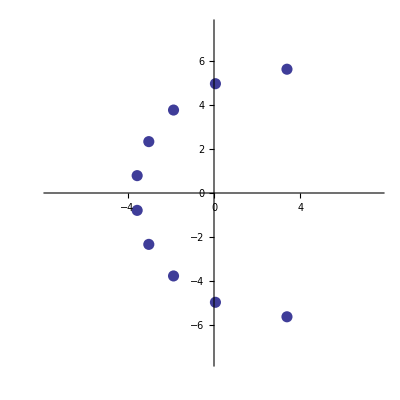

-Graphics-

```mathematica
RootsPlot[Exp[z],z,10]
RootsPlotOfPoly[exppoly10,z]
```

### Other

## Zeros

In this section we give some pictures of some entire functions without any zeros and some entire functions with zeros.

### Entire Functions without any zeros

Exponential

```mathematica
Exp[z]
```

ⅇ^z

Exp[polynomila] , Exp[z^n] Exp[z^2+1], Exp[(z-1)(z-2)(z-3)], Exp[z^5+z^4+z^3+z^2+z+1]

```mathematica
exppowertable=Table[Exp[z^k],{k,1,5}]
```

{ⅇ^z,ⅇ^(z^2),ⅇ^(z^3),ⅇ^(z^4),ⅇ^(z^5)}

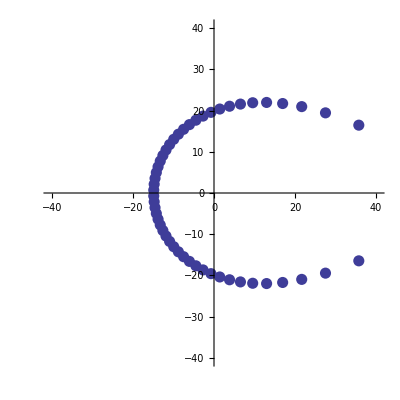
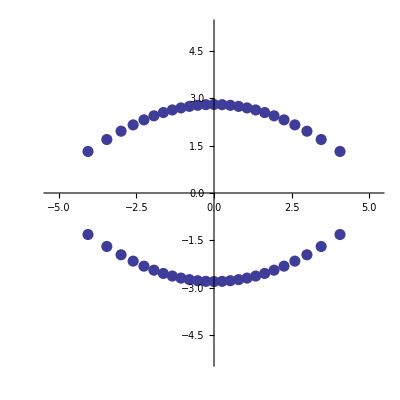
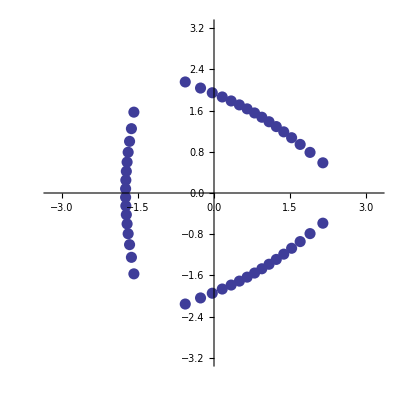
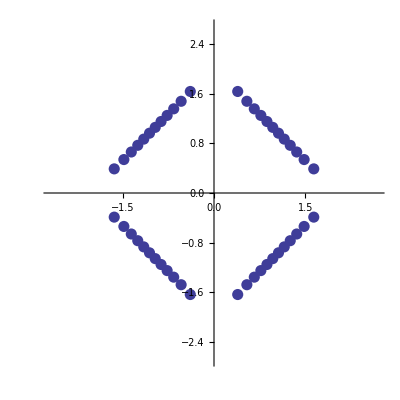
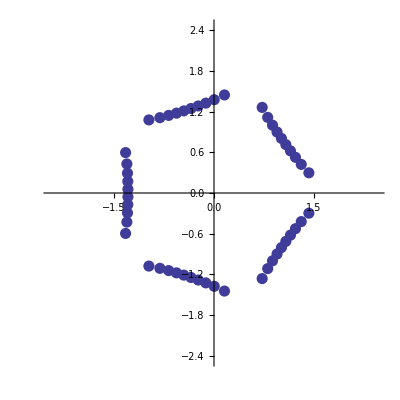

```mathematica
Table[RootsPlot[exppowertable[[k]],z,50],{k,1,5}]
```

```mathematica
expsomepolys = {Exp[z^2+1],Exp[(z-1)(z-2)(z-3)],Exp[z^5+z^4+z^3+z^2+1]}
```

{ⅇ^(1+z^2),ⅇ^((-3+z) (-2+z) (-1+z)),ⅇ^(1+z^2+z^3+z^4+z^5)}

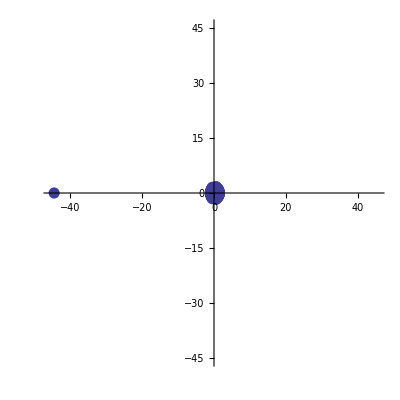
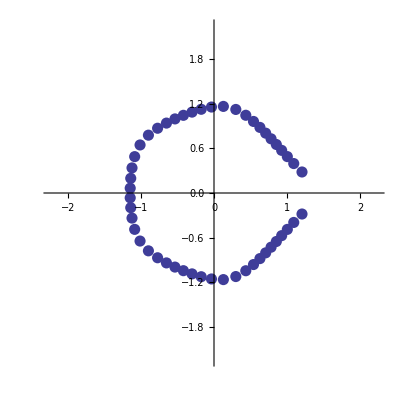
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[RootsPlot[expsomepolys[[k]],z,50],{k,1,3}]
```

Entire Functions Not of Finite Order: Exp[Exp[z]], Exp[Sin[z]], Exp[Sin[z]Cos[z]]

```mathematica
notfinitelist = {Exp[Exp[z]],Exp[Sin[z]],Exp[Sin[z] Cos[z]]}
```

{ⅇ^(ⅇ^z),ⅇ^Sin[z],ⅇ^(Cos[z] Sin[z])}

```mathematica
Table[RootsPlot[notfinitelist[[k]], ]]
```

### Some Special Functions

1/Gamma[z]

Sin,Cosine, Hyperbolic Sine, Hyperbolic Cosine

Exponential Sums

```mathematica
1/Gamma[z]
```

1/Gamma[z]

```mathematica
RootsPlot[1/Gamma[z],z,50]
```

RootsPlot[1/Gamma[z],z,50]

```mathematica
nodes={2 ,  Exp[I Pi/3], -3,  5 Exp[I Pi+ I Pi/4], -1-8I , 5 Exp[- I Pi/4]};
listnodes = Transpose[{Re[nodes],Im[nodes]}];
```

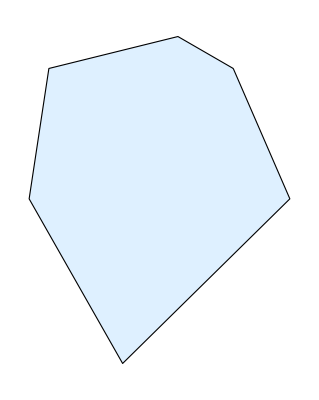

```mathematica
Graphics[{EdgeForm[Black],LightBlue,Polygon[listnodes]}]
```

```mathematica
expsum = Sum[Exp[nodes[[k]] z],{k,1,6}]
```

ⅇ^(-3 z)+ⅇ^((-1-8 ⅈ) z)+ⅇ^(2 z)+ⅇ^(5 ⅇ^(-(ⅈ π)/4) z)+ⅇ^(ⅇ^((ⅈ π)/3) z)+ⅇ^(5 ⅇ^(-(3 ⅈ π)/4) z)

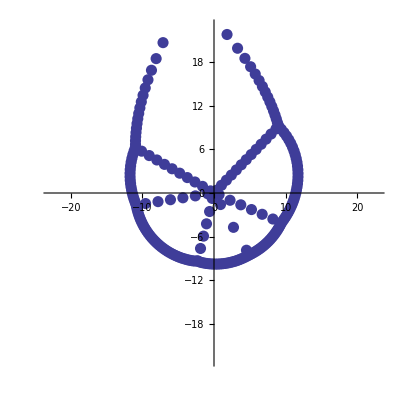

```mathematica
RootsPlot[expsum,z,200]
```

Airy Function

```mathematica
AiryAi[z]
```

AiryAi[z]

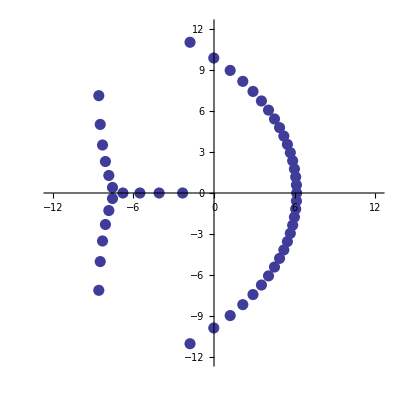

```mathematica
RootsPlot[AiryAi[z],z,50]
```

Erf

```mathematica
Erf[z]
```

Erf[z]

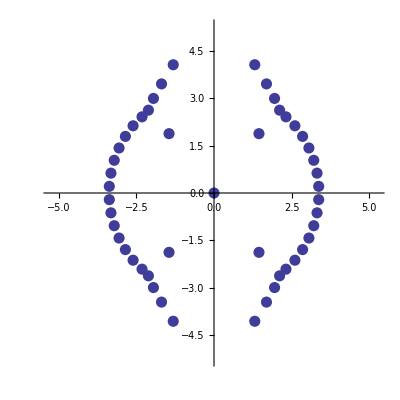

```mathematica
RootsPlot[Erf[z],z,50]
```

Some functions from Series Representations.

```mathematica
alog[z_,n_] = Sum[z^k /(Log[k+2])^k,{k,0,n}]
```

∑_(k=0)^n z^k Log[2+k]^-k

```mathematica
polyalog = alog[z,50];
```

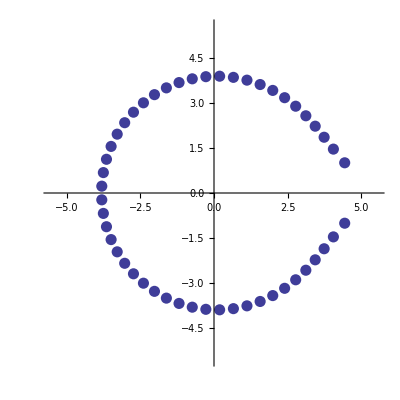

```mathematica
RootsPlotOfPoly[polyalog,z]
```

```mathematica
aloglog[z_,n_] = Sum[z^k / (Log[Log[k+2]])^k, {k,0,n}]
```

∑_(k=0)^n z^k Log[Log[2+k]]^-k

```mathematica
almostExp[z_,n_]=1+Sum[z^k/( k^k Exp[-k] Sqrt[2 Pi k]),{k,0,n}]
```

1+∑_(k=0)^n (ⅇ^k k^(-1/2-k) z^k)/(√(2 π))

Products of Functions we have already seen